## Тест 1

#### Тысячные

```mathematica
ClearAll["Global`*"]
NotebookDirectory[];
n = 2;
plots=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Pois_eq.txt"]],Table[Real,n+1]];
```

```mathematica
ListPlot3D[plots, PlotRange->All, AxesLabel->Automatic, ColorFunction->"Rainbow"]
```

-Graphics3D-

#### Решение

```mathematica
ClearAll["Global`*"]
NotebookDirectory[];
n = 2;
plots=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Pois_eq.txt"]],Table[Real,n+1]];
```

```mathematica
ListPlot3D[plots, PlotRange->All, AxesLabel->Automatic, ColorFunction->"Rainbow"]
```

-Graphics3D-

## Точное решение тест 2

```mathematica
ClearAll["Global`*"]
```

```mathematica
L=1;
```

```mathematica
Plot3D[1+x2,{x1,0,L},{x2,0,L},PlotRange->All,ColorFunction->"Rainbow"]
```

-Graphics3D-

## Точное решение тест 3

```mathematica
ClearAll["Global`*"]
```

```mathematica
L=1;
```

```mathematica
Plot3D[x1^2+x2^2,{x1,0,L},{x2,0,L},PlotRange->All,ColorFunction->"Rainbow"]
```

-Graphics3D-

## Точное решение (одна температура на концах, нелинейное K)

```mathematica
ClearAll["Global`*"]
```

```mathematica
c=1;ρ=1;u0 = 0.0;L=π;T=1;
α = 0.5;β =0.5;γ =2;Q=(*10*)0;t0=0.5;
```

```mathematica
K[x_]:= α+β x^γ;
ut0[x_]:=(*u0-x(L-x)*)Sin[x];
P[t_]:=t;
```

```mathematica
sol = NDSolve[{c ρ D[u[t,x],t]==D[K[u[t,x]]*D[u[t,x],x],x],u[0,x]==ut0[x],u[t,0]==u0, K[u[t,L]]Derivative[0,1][u][t,L]==P[t]},u,{t,0,T},{x,0,L}]
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

{{u→InterpolatingFunction[…]}}

```mathematica
Plot3D[Evaluate[u[t,x]/.First[sol],{t,0,T},{x,0,L}],PlotRange->All,ColorFunction->"Rainbow"]
```

-Graphics3D-

## Квазилинейное из методички

```mathematica
Clear["Global`*"]
```

```mathematica
σ = 2;κ = 0.5;c = 5;T = 2.0;L=10;
u0 = ((σ c^2)/κ)^(1/σ);
u[x_,t_]:=If[x≤c t,(σ c κ^-1(c t - x))^(1/σ),0];
Plot3D[Evaluate[u[x,t],{t,0,T},{x,0,L}],PlotRange->All,ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
i=1+(10/0.2+1)*0.9/0.0002;
Diff=Table[{plots⟦k⟧⟦2⟧,Abs[u[plots⟦k⟧⟦2⟧,plots⟦k⟧⟦1⟧]-plots⟦k⟧⟦3⟧]},{k,i,i+10/0.2}];
```

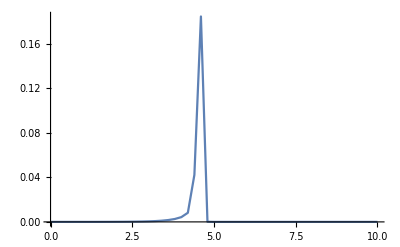

```mathematica
ListLinePlot[Diff,PlotRange->All]
```

```mathematica
n=10/0.2;i=1/0.0002;
```

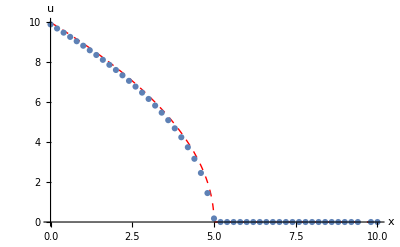

```mathematica
w=Show[Plot[u[x,1],{x,0,L},PlotStyle->{Red,Dashed,Thick}],ListPlot[plots[[1+n*i;;n+n*i,2;;3]]],AxesLabel->{"x","u"},PlotRange->All]
```

## Проверка порядков

```mathematica
ClearAll["`*"];
```

```mathematica
ω=1;tk=1.0;
 DSolve[{D[u[x,t],t]==1/ω D[u[x,t],{x,2}],u[x,0]==2Sin[ω x],u[0,t]==0,u[π/(2ω),t]==2Exp[-ω t]},u[x,t],x,t]⟦1⟧⟦1⟧⟦2⟧;
```

```mathematica
Sol[x_,t_]=%;
```

```mathematica
NotebookDirectory[];
n = 2;
For[i=1,i≤5,i++,len=0;
Subscript[plots, i]=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Integro_interpolation_mult_1.000000_"<>ToString[2^i]<>".000000.txt"]],Table[Real,n+1]];
Subscript[Diff, i]= Table[Abs[Sol[Subscript[plots, i]⟦k⟧⟦2⟧,Subscript[plots, i]⟦k⟧⟦1⟧]-Subscript[plots, i]⟦k⟧⟦3⟧],{k,1,Length[Subscript[plots, i]]}];Subscript[Err, i] = Max[Subscript[Diff, i]];]
```

```mathematica
GridData=Join[{{"τ, h","AbsErr(τ, h)","Δ", "log_qΔ"}},Table[{{0.1 * (1/2)^(j-1),0.1*1/2^(j-1)},Subscript[Err, j],Subscript[Err, j]/Subscript[Err, j-1],-Log[Subscript[Err, j]/Subscript[Err, j-1]]/Log[2]},{j,1,5}]];
```

```mathematica
GridData⟦2⟧⟦3⟧=0;
GridData⟦2⟧⟦4⟧=0;
```

```mathematica
Grid[GridData,Frame->All]
```

τ, h | AbsErr(τ, h) | Δ | log_qΔ
{0.1,0.1} | 0.00654447 | 0 | 0
{0.05,0.05} | 0.00281905 | 0.430754 | 1.21506
{0.025,0.025} | 0.000860095 | 0.305101 | 1.71264
{0.0125,0.0125} | 0.000209965 | 0.244119 | 2.03435
{0.00625,0.00625} | 0.0000525069 | 0.250074 | 1.99957

## Количество итераций

```mathematica
NotebookDirectory[];
n = 1;
plots=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Non_linear_iter.txt"]],Table[Real,n+1]];
```

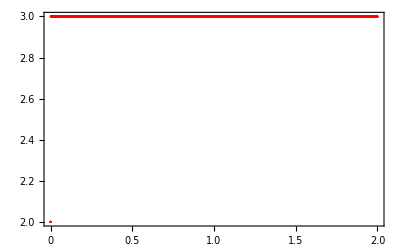

```mathematica
ListPlot[plots,PlotStyle->Red,PlotTheme->"Web"]
```